```mathematica
AN1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d0.02-2nd1.txt",{Number,Number}];
```

```mathematica
-----------
```

```mathematica
gapmax=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gap/GapD.d.0.075.p0.1.v11e4-e5-e6-e3-max.txt",{Number,Number}];
```

```mathematica
ClearAll[g,v1,v,v2]
```

```mathematica
d=0.08;
ClearAll[g,v1,v,v2]
ClearAll[a,b,p,g,m,α]
m=9;
v1[m-3]=p*p;
v1[m-2]=p*(1-p);
v1[m-1]=1-p;
v[m-2]=p*p;
v[m-1]=p*(1-p);
v[m]=1-p;
v2[m-3]=a*p*p;
v2[m-2]=a*p*(1-p)+(1-a)*p*p;
v2[m-1]=a*(1-p)+(1-a)*p*(1-p);
v2[m]=(1-a)*(1-p);
For [i=m+3,i<1001,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]
g[m-1]=α;
a=0;
α=p(1-p)/(1/d-m-0.5);
p=0.1;
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][m+2];
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])},{x,y}]
```

{{x→0.177118-0.0145773 b,y→0.0934275-0.0276157 b}}

```mathematica
g[m]=0.28983025400206297-0.0012745253976972927 b;
g[m+1]=0.15288134304953432-0.002411029918458674 b;
Solve[Sum[g[x],{x,m-1,200}]==1,b]
```

{{b→-34.7731}}

```mathematica
b=-34.77305996179277;
data=Table[{i+1,g[i]},{i,m-1,300}];
```

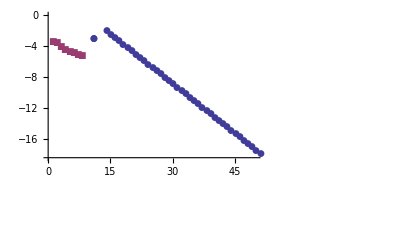

```mathematica
ListLogPlot[{data,gapmax},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{0,50},{10^-8,1}},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.075",AxesLabel->{"d","Pg"}]
```

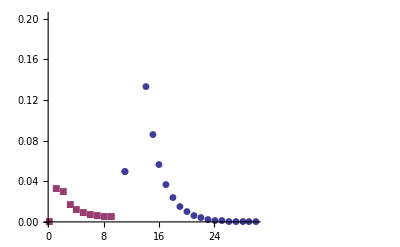

```mathematica
ListPlot[{data,gapmax},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{0,30},Full},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.075",AxesLabel->{"d","Pg"}]
```

```mathematica
d=0.02;
ClearAll[a,b,p,g,m,α]
m=11;
v1[m-3]=p*p;
v1[m-2]=p*(1-p);
v1[m-1]=1-p;
v[m-2]=p*p;
v[m-1]=p*(1-p);
v[m]=1-p;
v2[m-3]=a*p*p;
v2[m-2]=a*p*(1-p)+(1-a)*p*p;
v2[m-1]=a*(1-p)+(1-a)*p*(1-p);
v2[m]=(1-a)*(1-p);
For [i=m+3,i<1001,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]
g[m-1]=α;
a=0;
α=p(1-p)/(1/d-m-0.5);
p=0.1;
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][m+2];
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])},{x,y}]
```

{{x→-(-1. (-0.00191268-1. (0.000021039-0.716531 b) (0.+0.01 9[11])) (1.-1. (0.01 9[9]+0.09 9[10]+0.9 9[11]))-1. (-0.000191455+0.698392 b (0.+0.01 9[11])-1. (0.000021039-0.716531 b) (0.+0.01 9[10]+0.09 9[11])) (0.+0.01 9[10]+0.09 9[11]))/(-1. (1.-1. (0.01 9[9]+0.09 9[10]+0.9 9[11]))^2+1. (0.09 9[9]+0.9 9[10]) (0.+0.01 9[10]+0.09 9[11])),y→(1. (-0.00191268-1. (0.000021039-0.716531 b) (0.+0.01 9[11])))/(0.+0.01 9[10]+0.09 9[11])-(1. (-1. (-0.00191268-1. (0.000021039-0.716531 b) (0.+0.01 9[11])) (1.-1. (0.01 9[9]+0.09 9[10]+0.9 9[11]))-1. (-0.000191455+0.698392 b (0.+0.01 9[11])-1. (0.000021039-0.716531 b) (0.+0.01 9[10]+0.09 9[11])) (0.+0.01 9[10]+0.09 9[11])) (1.-1. (0.01 9[9]+0.09 9[10]+0.9 9[11])))/((-1. (1.-1. (0.01 9[9]+0.09 9[10]+0.9 9[11]))^2+1. (0.09 9[9]+0.9 9[10]) (0.+0.01 9[10]+0.09 9[11])) (0.+0.01 9[10]+0.09 9[11]))}}

```mathematica
g[m]=0.013801440666764905-0.24648790042619045 b;
g[m+1]=0.007280063954739728-0.46840926132255556 b;
Solve[Sum[g[x],{x,m-1,200}]==1,b]
```

{{b→-0.0339187}}

```mathematica
b=-0.033918683744783594;
data=Table[{i+1,g[i]},{i,m-1,300}];
```

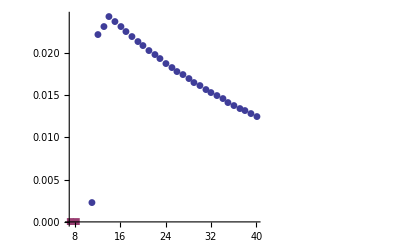

```mathematica
ListPlot[{data,gap8},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,40},Full},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.02",AxesLabel->{"d","Pg"}]
```

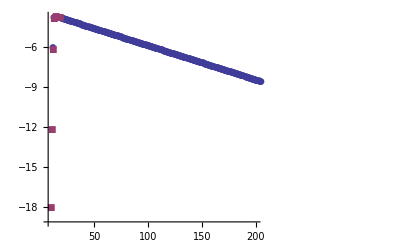

```mathematica
ListLogPlot[{data,gap8},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.2,0.3},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,200},Full},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.02",AxesLabel->{"d","Pg"}]
```

```mathematica
gapmax2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e7-2e2-max.txt",{Number,Number}];
```

```mathematica
************************************************************
```

```mathematica
ClearAll[a,b,p,α,pg]
m=11;

For [i=m+2,i<501,i++,
g[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]

g[m-1]=α;
a=0;
d=0.02;
α=p/(1/d-m-0.5);
p=0.09;
```

```mathematica
Solve[{x-((1-2p-α(1-3p))α+(p+α(1-3p))y+α*p*g[m+2])/(2p+α(1-3p))==0,
y-(p(1-α)α+p(1-α)x+(p+α(1-3p))g[m+2])/(2p+α(1-3p))==0},{x,y}]
```

{{x→0.0148019-0.24426 b,y→0.00846944-0.48233 b}}

```mathematica
g[m]=0.01480187368343307-0.24425971904967309 b;
g[m+1]=0.008469440094818918-0.4823303630838504 b;
```

```mathematica
Solve[Sum[g[x],{x,m-1,500}]==1,b]
```

{{b→-0.0335638}}

```mathematica
b=-0.03356380759099609;
```

```mathematica
data=Table[{i+1,g[i]},{i,m-1,300}];
```

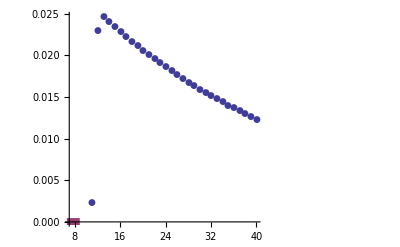

```mathematica
ListPlot[{data,gapmax2},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,40},Full},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.02",AxesLabel->{"d","Pg"}]
```

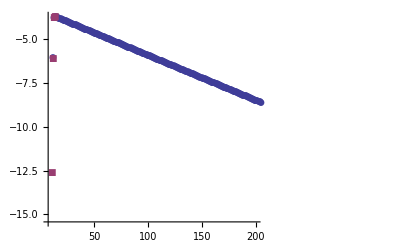

```mathematica
ListLogPlot[{data,gapmax2},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,200},Full},PlotLabel->"Gap Distribution Prob. Vmax=11 p=0.1 d=0.02",AxesLabel->{"d","Pg"}]
```

```mathematica
**********************************************************
```

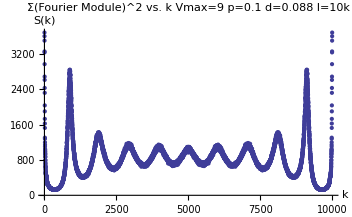

```mathematica
d="0.088";
l="10";
v="9";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
gf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ListPlot[fourier,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",PlotRange->Full,AxesLabel->{"k","S(k)"}]
```

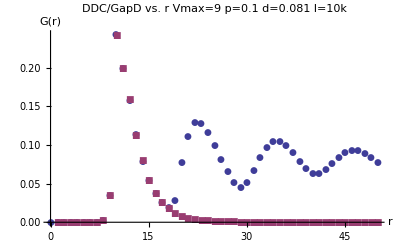

```mathematica
ListPlot[{ddc,gf},PlotRange->{{0,50},Full},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","G(r)"},PlotLegend->{"DDC(G(r))","Gap Disribution"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic]
```

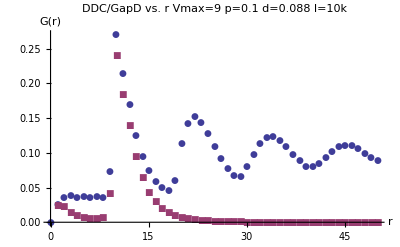

```mathematica
ListPlot[{ddc,gf},PlotRange->{{0,50},Full},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","G(r)"},PlotLegend->{"DDC(G(r))","Gap Disribution"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic]
```

```mathematica
***************************************************************
```

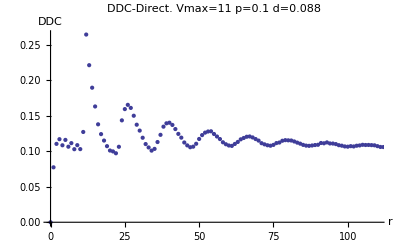

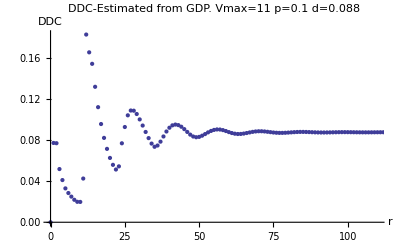

```mathematica
d="0.088";
p="0.1";
vmax="11";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
```

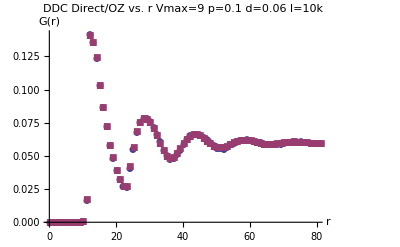

```mathematica
ListPlot[{DDC,DDCC},PlotRange->{{0,80},Full},PlotLabel->"DDC Direct/OZ vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","G(r)"},PlotLegend->{"G(r)-Direct","G(r)-OZ estimate"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic]
```

```mathematica
DDC={{0,1.08507*^-8},{1,0.0774139},{2,0.110457},{3,0.117051},{4,0.108471},{5,0.116044},{6,0.106472},{7,0.111503},{8,0.102953},{9,0.108653},{10,0.103062},{11,0.12724},{12,0.264524},{13,0.221342},{14,0.189618},{15,0.163176},{16,0.138008},{17,0.124206},{18,0.115131},{19,0.107239},{20,0.101086},{21,0.0998375},{22,0.0972236},{23,0.106351},{24,0.143589},{25,0.159458},{26,0.16545},{27,0.16114},{28,0.150103},{29,0.137457},{30,0.129157},{31,0.119089},{32,0.1102},{33,0.105407},{34,0.100958},{35,0.103396},{36,0.113057},{37,0.123212},{38,0.134715},{39,0.139417},{40,0.140281},{41,0.137138},{42,0.131329},{43,0.124519},{44,0.119235},{45,0.112411},{46,0.108333},{47,0.105717},{48,0.106533},{49,0.110607},{50,0.117368},{51,0.12281},{52,0.126281},{53,0.127878},{54,0.128188},{55,0.1244},{56,0.120858},{57,0.117253},{58,0.112694},{59,0.109925},{60,0.108165},{61,0.107597},{62,0.110318},{63,0.113164},{64,0.11686},{65,0.118749},{66,0.120489},{67,0.120894},{68,0.119517},{69,0.117271},{70,0.115085},{71,0.111428},{72,0.109786},{73,0.108504},{74,0.107862},{75,0.109025},{76,0.11156},{77,0.112356},{78,0.114849},{79,0.115693},{80,0.115437}};
DDCC={{0,0},{1,0.0774694},{2,0.0772126},{3,0.0519636},{4,0.041206},{5,0.033073},{6,0.028546},{7,0.025051},{8,0.0219521},{9,0.0199724},{10,0.0198634},{11,0.0426941},{12,0.183353},{13,0.165976},{14,0.154759},{15,0.132322},{16,0.112415},{17,0.0959438},{18,0.0824043},{19,0.0716837},{20,0.0628321},{21,0.0560798},{22,0.0515185},{23,0.0545988},{24,0.0771251},{25,0.0930327},{26,0.104448},{27,0.10914},{28,0.108974},{29,0.10574},{30,0.100459},{31,0.0944648},{32,0.0881979},{33,0.0821939},{34,0.0768445},{35,0.0737214},{36,0.0749649},{37,0.0787412},{38,0.083794},{39,0.0886459},{40,0.0923351},{41,0.0946522},{42,0.0954139},{43,0.0948885},{44,0.0933031},{45,0.0909655},{46,0.0882226},{47,0.0856054},{48,0.0837655},{49,0.0830578},{50,0.0833932},{51,0.0845613},{52,0.0861336},{53,0.0877875},{54,0.0891928},{55,0.0901901},{56,0.0906521},{57,0.0905635},{58,0.090004},{59,0.0891028},{60,0.0880675},{61,0.0871455},{62,0.0864931},{63,0.0862049},{64,0.0862669},{65,0.0866225},{66,0.0871541},{67,0.0877465},{68,0.0882871},{69,0.0886847},{70,0.0888877},{71,0.0888805},{72,0.0886835},{73,0.0883674},{74,0.0880014},{75,0.0876663},{76,0.08742},{77,0.0872956},{78,0.0872975},{79,0.0874079},{80,0.087592}};
```

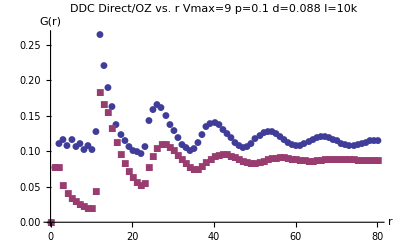

```mathematica
ListPlot[{DDC,DDCC},PlotRange->{{0,80},Full},PlotLabel->"DDC Direct/OZ vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","G(r)"},PlotLegend->{"G(r)-Direct","G(r)-OZ estimate"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic]
```

```mathematica
**************************************************************
```

```mathematica
d=0.088;
ClearAll[v,v1,v2]
ClearAll[a,b,p,g,m,α]
m=9;
v1[m-3]=p*p;
v1[m-2]=p*(1-p);
v1[m-1]=1-p;
v[m-2]=p*p;
v[m-1]=p*(1-p);
v[m]=1-p;
v2[m-3]=a*p*p;
v2[m-2]=a*p*(1-p)+(1-a)*p*p;
v2[m-1]=a*(1-p)+(1-a)*p*(1-p);
v2[m]=(1-a)*(1-p);
For [i=m+3,i<1001,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]
g[m-1]=α;
a=0;
α=p(1-p)/(1/d-m-0.5);
p=0.1;
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][m+2];
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])},{x,y}]
```

{{x→0.285118-0.00319139 b,y→0.150395-0.00603749 b}}

```mathematica
g[m]=0.2851175669451187-0.003191388417953891 b;
g[m+1]=0.15039546755279376-0.006037488887125254 b;
Solve[Sum[g[x],{x,m-1,200}]==1,b]
```

{{b→-14.0002}}

```mathematica
b=-14.00016704657431;
data=Table[{i+1,g[i]},{i,m-1,300}];
```

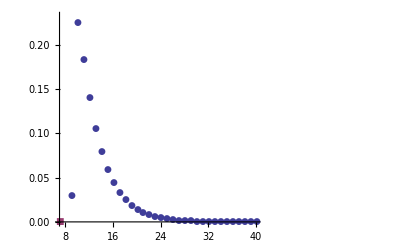

```mathematica
ListPlot[{data,gf},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,40},Full},PlotLabel->"Gap Distribution Prob. Vmax=9 p=0.1 d=0.08",AxesLabel->{"d","Pg"}]
```

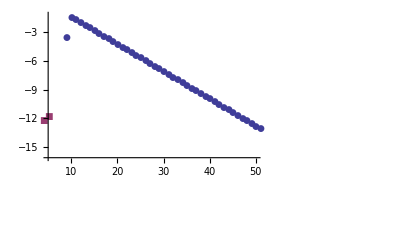

```mathematica
ListLogPlot[{data,gf},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.2,0.3},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{5,50},{10^-7,0.3}},PlotLabel->"Gap Distribution Prob. Vmax=9 p=0.1 d=0.08",AxesLabel->{"d","Pg"}]
```

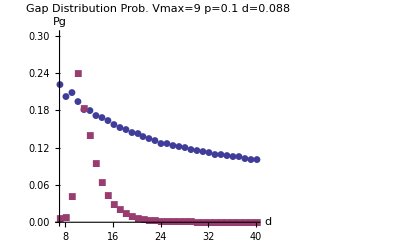

```mathematica
ListPlot[{data,gf},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.4,0.25},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{7,40},Full},PlotLabel->"Gap Distribution Prob. Vmax=9 p=0.1 d=0.088",AxesLabel->{"d","Pg"}]
```

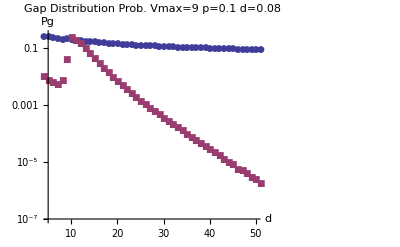

```mathematica
ListLogPlot[{data,gf},PlotLegend->{"Calculated","Simulation"},LegendPosition->{0.2,0.3},LegendSize->{0.5,0.2},LegendShadow->None,Joined->{False},PlotMarkers->Automatic,PlotRange->{{5,50},{10^-7,0.3}},PlotLabel->"Gap Distribution Prob. Vmax=9 p=0.1 d=0.08",AxesLabel->{"d","Pg"}]
```

```mathematica
gf={{1,0.0246274},{2,0.0232007},{3,0.0134905},{4,0.00966616},{5,0.00720621},{6,0.00610434},{7,0.00538301},{8,0.00719767},{9,0.0412645},{10,0.239666},{11,0.183154},{12,0.139086},{13,0.0947604},{14,0.0643901},{15,0.0432614},{16,0.029287},{17,0.0199305},{18,0.0136939},{19,0.00956134},{20,0.00671182},{21,0.00477845},{22,0.00345691},{23,0.0025178},{24,0.00184879},{25,0.00137792},{26,0.0010342},{27,0.000771534},{28,0.000585436},{29,0.000449848},{30,0.000346913},{31,0.000266117},{32,0.000205814},{33,0.000160814},{34,0.00012553},{35,0.0000951705},{36,0.00007520830000000001},{37,0.00005863640000000001},{38,0.00004465910000000001},{39,0.0000342424},{40,0.0000272538},{41,0.000021799200000000003},{42,0.0000171212},{43,0.0000123485},{44,9.356059999999999*^-6},{45,7.95455*^-6},{46,5.511359999999999*^-6},{47,5.03788*^-6},{48,4.01515*^-6},{49,2.85985*^-6},{50,2.34848*^-6},{51,1.79924*^-6},{52,1.19318*^-6},{53,1.1553*^-6},{54,7.95455*^-7},{55,4.7348499999999995*^-7},{56,4.5454499999999997*^-7},{57,5.681819999999999*^-7},{58,3.4090899999999997*^-7},{59,2.08333*^-7},{60,1.8939399999999998*^-7},{61,1.13636*^-7},{62,1.13636*^-7},{63,1.13636*^-7},{64,1.13636*^-7},{65,7.57576*^-8},{66,3.78788*^-8},{67,0},{68,3.78788*^-8},{69,0},{70,3.78788*^-8},{71,0},{72,0},{73,0},{74,1.89394*^-8},{75,0},{76,1.89394*^-8},{77,0},{78,0}};
```

```mathematica
gf={{1,2.58333*^-6},{2,3.3541699999999996*^-6},{3,3.9375*^-6},{4,5.10417*^-6},{5,7.83333*^-6},{6,0.000022562500000000003},{7,0.000133188},{8,0.00160625},{9,0.0327016},{10,0.231636},{11,0.193662},{12,0.156754},{13,0.113959},{14,0.0816201},{15,0.0574203},{16,0.0401264},{17,0.0278999},{18,0.0193707},{19,0.0133528},{20,0.00924215},{21,0.0063726},{22,0.00439537},{23,0.00303367},{24,0.00208087},{25,0.00142565},{26,0.000989271},{27,0.000679375},{28,0.000466312},{29,0.000322333},{30,0.00021825},{31,0.000153271},{32,0.000105},{33,0.00007197920000000001},{34,0.0000477708},{35,0.0000336667},{36,0.000023333300000000002},{37,0.000015375},{38,0.000011312500000000002},{39,7.83333*^-6},{40,4.979169999999999*^-6},{41,3.41667*^-6},{42,2.35417*^-6},{43,1.6458299999999997*^-6},{44,9.374999999999999*^-7},{45,6.666669999999999*^-7},{46,5.20833*^-7},{47,3.95833*^-7},{48,3.1249999999999997*^-7},{49,1.66667*^-7},{50,8.33333*^-8},{51,1.4583299999999998*^-7},{52,0},{53,4.16667*^-8},{54,0},{55,4.16667*^-8},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0},{101,0},{102,0},{103,0},{104,0},{105,0},{106,0},{107,0},{108,0},{109,0},{110,0},{111,0},{112,0},{113,0},{114,0},{115,0},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0}};
```